# Sistemas conservativos

## Ejemplo:

Consideremos el sistema mecánico , donde la energía potencial está dada por . Entonces, considerando que , y tomando , la ecución diferencial es:
. Definiendo , transformamos esta ecuación en el sistema


y la cantidad conservada es la energía, definida por
. 
Las soluciones son las curvas de nivel de la energía, como podemos observar:

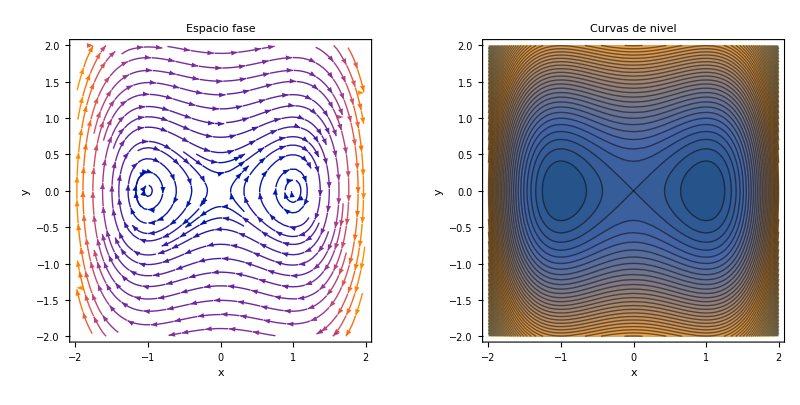

```mathematica
GraphicsRow[{StreamPlot[{y,x-x^3},{x,-2,2},{y,-2,2},FrameLabel->{x,y},PlotLabel->"Espacio fase"],ContourPlot[(y^2)/2-(x^2)/2+(x^4)/4,{x,-2,2},{y,-2,2},FrameLabel->{x,y},PlotLabel->"Curvas de nivel",Contours->50]}]
```

Podemos observar que los centros de la ecuación corresponden a mínimos de la energía:

```mathematica
Plot3D[(y^2)/2-(x^2)/2+(x^4)/4,{x,-1.5,1.5},{y,-1,1},AxesLabel->{x,y,"E"}]
```

-Graphics3D-